# Wolfram at UTEP

Manuel Aguilar

#### Create an Account

```mathematica
Hyperlink["https://account.wolfram.com/"]
```

https://account.wolfram.com/

#### Cloud Platform

```mathematica
Hyperlink["https://www.wolframcloud.com"]
```

https://www.wolframcloud.com

#### Mathematica UTEP Licence

```mathematica
Hyperlink["https://www.utep.edu/science/math/mathematica/"]
```

https://www.utep.edu/science/math/mathematica/

#### Mathematica Licence Form

```mathematica
Hyperlink["https://user.wolfram.com/portal/requestAK/b8063a17aa6dda6649b6c5f5fc4b738e21dff7c5"]
```

https://user.wolfram.com/portal/requestAK/b8063a17aa6dda6649b6c5f5fc4b738e21dff7c5

#### Interactive Courses

Learn New Skills

```mathematica
Hyperlink["https://www.wolfram.com/wolfram-u/"]
```

https://www.wolfram.com/wolfram-u/

Intro to Calculus

```mathematica
Hyperlink["https://www.wolfram.com/wolfram-u/introduction-to-calculus/what-is-calculus.html"]
```

https://www.wolfram.com/wolfram-u/introduction-to-calculus/what-is-calculus.html

Intro to Image Processing

```mathematica
Hyperlink["https://www.wolfram.com/wolfram-u/introduction-to-image-processing/course-overview.html"]
```

https://www.wolfram.com/wolfram-u/introduction-to-image-processing/course-overview.html

Multi-Paradigm Data Science

```mathematica
Hyperlink["https://www.wolfram.com/wolfram-u/multiparadigm-data-science/question.html?t=01"]
```

https://www.wolfram.com/wolfram-u/multiparadigm-data-science/question.html?t=01

Mathematica Student Certification Program

```mathematica
Hyperlink["https://www.wolfram.com/training/certification/students/"]
```

https://www.wolfram.com/training/certification/students/

## Basics

#### Everything is a list

```mathematica
list = {1,2,3,4};
```

```mathematica
numberList = Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
table  = Table[e,{e,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
#&/@Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

### Procedural

#### Do Loop

```mathematica
Do[Print[e],{e,10}]
```

#### For Loop

```mathematica
For[i=0,i<10,i++,Print[i]]
```

0

1

2

3

4

5

6

7

8

9

#### While Loop

```mathematica
i = 0;
```

```mathematica
While[10 > i, Print["i has thew value of: "<>ToString[i]]; i++;]
```

i has thew value of: 0

i has thew value of: 1

i has thew value of: 2

i has thew value of: 3

i has thew value of: 4

i has thew value of: 5

i has thew value of: 6

i has thew value of: 7

i has thew value of: 8

i has thew value of: 9

#### If Statement

```mathematica
If[i = 2; i>0,"i is greater than 2",False]
```

i is greater than 2

### Recursion

#### Fibonacci Sequence

```mathematica
Clear[f]
```

```mathematica
f[n_]:=1 /; n==1 
f[n_]:=1 /;n==2
f[n_]:=f[(n-2)] + f[(n-1)]/; n≥2
```

```mathematica
?f
```

#### Trace Fibonacci Sequence

```mathematica
TracePrint[f[4],f[_Integer] | f[_] + f[_]]
```

f[4]

f[4-2]+f[4-1]

f[2]

f[3]

f[3-2]+f[3-1]

f[1]

f[2]

3

#### Factorial

```mathematica
Clear[f]
```

```mathematica
f[n_] := 1 /; n==0; 
f[n_] := n* f[n-1];
```

```mathematica
?f
```

#### Trace Factorial Sequence

```mathematica
TracePrint[f[4],f[_] | f[_] * f[_]]
```

f[4]

f[4-1]

f[3]

f[3-1]

f[2]

f[2-1]

f[1]

f[1-1]

f[0]

24

#### Plot Sequences

```mathematica
Manipulate[ListPlot[Accumulate[Table[f[n],{n,i}]],Filling->Axis,AxesOrigin->{0,0},AspectRatio->1/2],{{i,10,"nth Fibonacci"},3,1000,1}]
```

### Documentation

```mathematica
?Do
```

```mathematica
?For
```

```mathematica
?While
```

```mathematica
?If
```

```mathematica
?Switch
```

## Time Series

```mathematica
init = DateObject[{2019,8,1,12,0,0}]
```

Thu 1 Aug 2019 12:00:00GMT-7.

```mathematica
final = DateObject[{2019,12,1,12,0,0}]
```

Sun 1 Dec 2019 12:00:00GMT-7.

### Get Time Series

```mathematica
?WeatherData
```

```mathematica
?FinancialData
```

### Using Time Series Data

```mathematica
WeatherData["AGGH","Temperature",{init,final}]
```

TimeSeries[…]

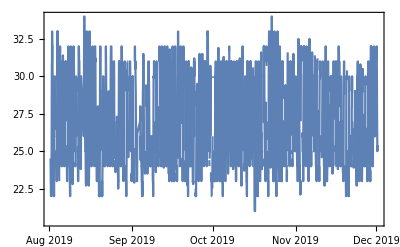

```mathematica
DateListPlot[WeatherData["AGGH","Temperature",{init,final}]]
```

```mathematica
humidity = Tooltip[Normal[WeatherData["ASLH","Humidity",#]],#]&/@DateRange[init,final];
```

```mathematica
GraphicsRow[{ListPlot[humidity,PlotLabel->"Humidity"],GeoGraphics[GeoMarker[WeatherData["ASLH","Coordinates"]]]}]
```

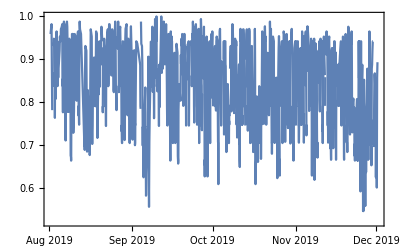

```mathematica
DateListPlot[WeatherData["AGGM","Humidity",{init,final}]]
```

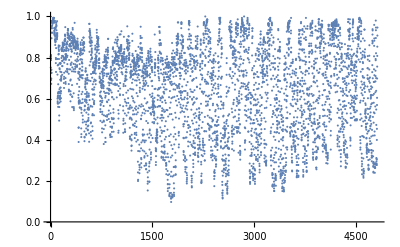

```mathematica
ListPlot[#⟦2⟧&/@Normal[WeatherData["ABBANF","Humidity",{init,final}]]]
```

```mathematica
test = WeatherData["AGGM","Humidity",{init,final}];
```

```mathematica
test2 = WindSpeedData["KJFK",{init,final}];
```

### Financial Data

```mathematica
stocks1 = FinancialData["NASDAQ:TSLA",{DateObject[{2019,12,1,12,0,0}],DateObject[{2019,12,31,24,0,0}]}];
stocks2 = FinancialData["NASDAQ:NFLX",{DateObject[{2019,12,1,12,0,0}],DateObject[{2019,12,31,24,0,0}]}];
```

```mathematica
stocks3= FinancialData["NASDAQ:AMZN",{DateObject[{2019,12,1,12,0,0}],DateObject[{2019,12,31,24,0,0}]}];
```

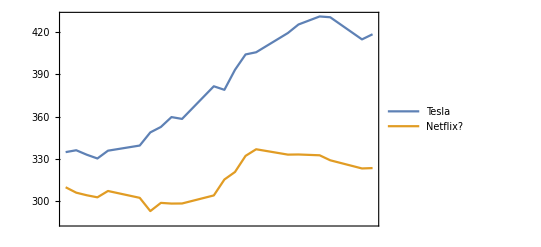

```mathematica
DateListPlot[{stocks1,stocks2,stocks3},PlotLegends->{"Tesla","Netflix","Amazon"}]
```

#### Time Series Objects

```mathematica
MatrixForm[stocks1["Properties"]]
```

(DatePath
Dates
FirstDate
FirstTime
FirstValue
LastDate
LastTime
LastValue
Path
PathFunction
PathLength
Times
ValueDimensions
Values)

## Mathematics

#### Mathematical TypeSetting

```mathematica
Hyperlink["https://reference.wolfram.com/language/guide/MathematicalTypesetting.html"]
```

https://reference.wolfram.com/language/guide/MathematicalTypesetting.html

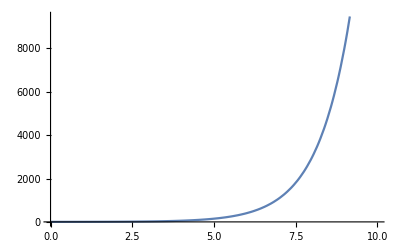

```mathematica
Plot[ⅇ^x,{x,0,10}]
```

```mathematica
∫_0^1 (2*x^2)/√xⅆx
```

4/5

```mathematica
∫(3*x)ⅆx
```

(3 x^2)/2

```mathematica
∑_(i=0)^10 (i+2)/2
```

77/2

```mathematica
SphericalPlot3D[1+2 Cos[2 θ],{θ,0,Pi},{ϕ,0,2 Pi},PlotTheme->"Detailed"]
```

-Graphics3D-

```mathematica
a = CharacterRange["a","c"]; 
b = CharacterRange["a","d"];
```

```mathematica
a ∪ b
```

{a,b,c,d}

```mathematica
a ∩ b
```

{a,b,c}

### Solving Systems of Linear Equations

```mathematica
Grid[{
"Solving for "<> ToString[#],
Flatten@Solve[x^2  + 2 == y^3 +1 , #]}&/@{x,y},
Spacings->{3,2}]
```

Solving for x | {x→-√(-1+y^3),x→√(-1+y^3)}
Solving for y | {y→(1+x^2)^(1/3),y→-(-1)^(1/3) (1+x^2)^(1/3),y→(-1)^(2/3) (1+x^2)^(1/3)}

### Plotting Functions

```mathematica
f[x_] = 2*x^2 +2*x-1; 
g[x_] = x^2+3*x+1;
```

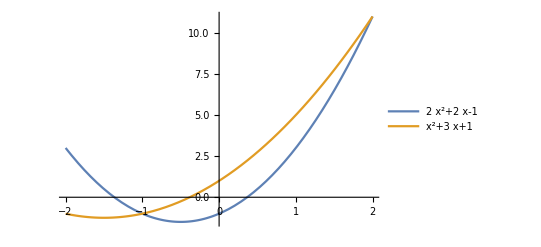

```mathematica
Plot[{f[x],g[x]},{x,-2,2},
PlotLegends->{f[x],g[x]}]
```

```mathematica
Manipulate[Plot[trigFunction[x],{x,-2*π,2*π}],{trigFunction,{Sin,Cos,Tan,Csc}}]
```

```mathematica
Manipulate[RevolutionPlot3D[t^a-t^b,{t,0,1}],{a,0,5,1},{b,0,5,1}]
```

```mathematica
ContourPlot3D[x^3+y^2-z^2==0,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

### Calculus

```mathematica
Grid[
Partition[
{
"Derivative",HoldForm[D[2*x^2 +2*x-1,x]],D[f[x],x],
"Integral",HoldForm[Integrate[2*x^2+2*x-1,x]],Integrate[2*x^2+2*x-1,x],
"",HoldForm[Integrate[2*x^2 +2*x-1,{x,0,1}]],NIntegrate[2*x^2 +2*x-1,{x,0,1}],
"Summation",HoldForm[Sum[2*x^2 +2*x-1,{x,1,100}]],Sum[2*x^2 +2*x-1,{x,1,100}],
"Limits",HoldForm[Limit[2*x^2+2*x-1,x -> Infinity]],Limit[2*x^2+2*x-1,x -> Infinity],
"",HoldForm[Limit[2*x^2+2*x-1,x -> 100]],Limit[2*x^2+2*x-1,x -> 100]
},3]
,Spacings->{10,2}]
```

Derivative | ∂_x (2 x^2+2 x-1) | 2+4 x
Integral | ∫(2 x^2+2 x-1)ⅆx | -x+x^2+(2 x^3)/3
 | ∫_0^1 (2 x^2+2 x-1)ⅆx | 0.666667
Summation | ∑_(x=1)^100 (2 x^2+2 x-1) | 686700
Limits | lim_(x→∞) (2 x^2+2 x-1) | ∞
 | lim_(x→100) (2 x^2+2 x-1) | 20199

### Truth Tables

```mathematica
Manipulate[
TableForm[BooleanTable[{p,q,r}->x,{p,q,r}]],
{x,""}
]
```

### Set Theory

```mathematica
s1= CharacterRange["a","e"]; 
s2 = CharacterRange["a","h"];
```

```mathematica
TableForm[{{"Set 1:",TraditionalForm@s1},{"Set 2:",TraditionalForm@s2}}]
```

Set 1: | {a,b,c,d,e}
Set 2: | {a,b,c,d,e,f,g,h}

#### Union

```mathematica
Union[s1,s2]
```

{a,b,c,d,e,f,g,h}

#### Intersection

```mathematica
Intersection[s1,s2]
```

{a,b,c,d,e}

#### Complement

```mathematica
universe = CharacterRange["a","z"];
```

```mathematica
Complement[universe,s1,s2]
```

{i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
s = CharacterRange["a","c"]
```

{a,b,c}

#### Subsets

```mathematica
Subsets[s]
```

{{},{a},{b},{c},{a,b},{a,c},{b,c},{a,b,c}}

### Find Equational Proofs in Boolean Logic

```mathematica
Column[axioms=AxiomaticTheory[{"BooleanAxioms",<|"And"->and,"Or"->or,"Not"->not|>}]]
```

∀_{a,b}and[a,b]==and[b,a]
∀_{a,b}or[a,b]==or[b,a]
∀_{a,b}and[a,or[b,not[b]]]==a
∀_{a,b}or[a,and[b,not[b]]]==a
∀_{a,b,c}and[a,or[b,c]]==or[and[a,b],and[a,c]]
∀_{a,b,c}or[a,and[b,c]]==and[or[a,b],or[a,c]]

```mathematica
proof=FindEquationalProof[ForAll[{a,b},or[not[or[not[a],b]],not[or[not[a],not[b]]]]==a],axioms]
```

ProofObject[…]

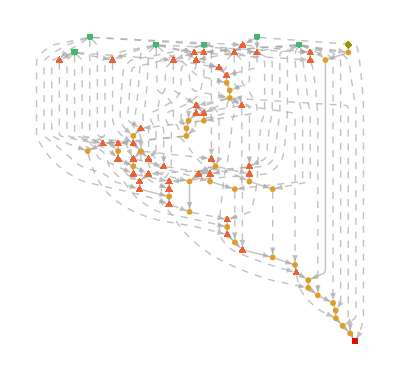

```mathematica
proof["ProofGraph"]
```

#### Second Example

```mathematica
proof=FindEquationalProof[a==c,{a==b,b==c}]
```

ProofObject[…]

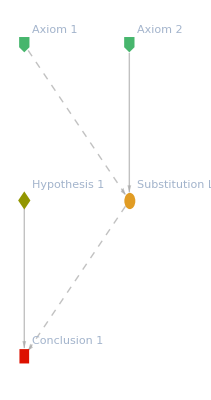

```mathematica
proof["ProofGraph"]
```

```mathematica
proof["ProofNotebook"]
```

Axiom 1
We are given that:
b==a
Axiom 2
We are given that:
b==c
Hypothesis 1
We would like to show that:
a==c
Substitution Lemma 1
It can be shown that:
a==c
Proof
We start by taking Axiom 2, and apply the substitution:
b→a
which follows from Axiom 1.
Conclusion 1
We obtain the conclusion:
True
Proof
Take Hypothesis 1, and apply the substitution:
a→c
which follows from Substitution Lemma 1.

## Cartography

```mathematica
WeatherData["WMO27648","Coordinates"] //GeoPosition //GeoMarker //GeoGraphics
```

-Graphics-

```mathematica
Partition[GeoGraphics[GeoRange->"World",GeoProjection->#,GeoGridLines->Automatic,PlotLabel->#]&/@{"Albers","Armadillo","Bonne","Mercator","WinkelTripel","Mollweide","Orthographic","Wiechel","LambertAzimuthal"},3]//Grid
```

-Graphics-

```mathematica
Manipulate[
GeoGraphics[
Table[
GeoMarker@RandomGeoPosition[Entity["Country",name]],{e,number}],GeoBackground->t],
{{t,Automatic,"Theme"},{"Satellite","ReliefMap","ContourMap","Coastlines"}},
{{name,"UnitedStates","Country"},{"UnitedStates","Mexico","Germany","France","UnitedKingdom"}},
{{number,3,"Number of Markers"},1,10,1},ContinuousAction->False]
```

```mathematica
geo2 = Table[RandomGeoPosition[Entity["Country","Canada"]],{e,10}];
```

```mathematica
GeoGraphics[GeoMarker[geo2]]
```

-Graphics-

## Chemistry

```mathematica
m=Molecule["3'-deoxy-3'-[(L-methionyl-L-phenylalanyl)amino]adenosine 5'-(dihydrogen phosphate)"]
```

Molecule[…]

### Chemical Visuals

```mathematica
{
MoleculePlot[m],
MatrixPlot@m["GraphDistanceMatrix"]
}//GraphicsRow
```

-Graphics-

```mathematica
myricetin=Molecule["3,5,7-trihydroxy-2-(3,4,5-trihydroxyphenyl)-4-chromenone"]
```

Molecule[…]

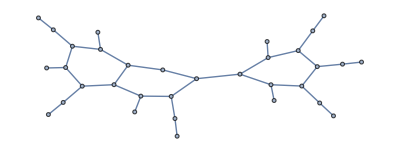

```mathematica
graph=MoleculeGraph[myricetin]
```

```mathematica
cycle = FindFundamentalCycles[graph];
partition = FindGraphPartition[graph];
communities=FindGraphCommunities[MoleculeGraph[myricetin],Method->"Spectral"];
```

```mathematica
GraphicsGrid[{{"Molecule Plot",MoleculePlot3D[myricetin]},{"Fundamental Cycles",MoleculePlot3D[myricetin,cycle]},{"Partition",MoleculePlot[myricetin,partition]},{"Communities",MoleculePlot[myricetin,Map[BondList[myricetin,#]&,communities]]}},ImageSize->{1000,1000}]
```

-Graphics-

## Mailing List

```mathematica
Hyperlink["https://wolfr.am/JTPFT8qA"]
```

https://wolfr.am/JTPFT8qA